# Remnant-Plot

Ein Plot über Remnants, original aus Calc7 (22.02.2014) kopiert und angepasst am 19.07.2014.
Da der Plot eher das Prinzip statt konkreter Metriken erläutern soll, geht es nicht um Extradimensionen oder so.

```mathematica
holo[z_]:=z^2/(z^2 +1)
halpha[z_,α_] := 1/(1+(1/z)^α / 2)^ (3/α)
SMM[z_]=1; (* Schwarzschild *)
α0 = 3/Log[2] * Log[3/2];
g00[z_, M_, func_] := 1 - 2M func[z]/z
```

```mathematica
(* Vorbereitungen fuer den Export *)
SetDirectory[NotebookDirectory[]];
cm=72/2.54;
```

## Neu: Holo-Plot für Remnant

### Vorbereitendes für den Plot

```mathematica
(* Labels direkt auf Funktionen anzeigen *)
ClearAll[EpiLabels]
EpiLabels[xpoint_,data_, labels_]:= 
With[{xpoints=If[Head@xpoint===List, xpoint, xpoint&/@ labels]}, (* erlaube Liste von xpoints *)
Text[
Rotate[labels⟦#⟧,ArcTan[ data'[xpoints⟦#⟧]⟦#⟧ ],{Left,Bottom}],
{xpoints⟦#⟧, 0 + data[xpoints⟦#⟧]⟦#⟧},
Background -> White
(* Opacity[0.8,White]*)
] & /@ Range@Length@data@1] (* 1: any value to introspect list*)
RootToSol[root_] := root/. {{_ -> y_}-> y} (* Extrahieren von FindRoot-Ergebnissen *)
```

```mathematica
masses = {0.5, 1.0, 1.5};
ClearAll[holoGraphs];
holoGraphs[z_] = Join[g00[z,#,holo]&/@masses] (* must be function for EpiLabels *)
SMMGraphs = Join[g00[z,#,SMM] & /@masses]
holoCompareFuncs= Join[holoGraphs[z],SMMGraphs];
```

{1-(1. z)/(1+z^2),1-(2. z)/(1+z^2),1-(3. z)/(1+z^2)}

{1-1./z,1-2./z,1-3./z}

```mathematica
holoLabels = "M="<>ToString@NumberForm[#,{2,1}]<>"M_0" &/@masses;
holoColors = {Blue, Darker@Green, Red};
(* Colors of Penrose diagram: r+, r-, r=0, r*=Darker@Green *)
pointColors = RGBColor@@@ ({ {255,0,224}, {0,145,170},{204,0,0},{0,170,0}}/255);
(* die pointColors werden jetzt doch nicht mehr verwendet, da sie den Plot sehr unverstaendlich machen *)
```

### Plot

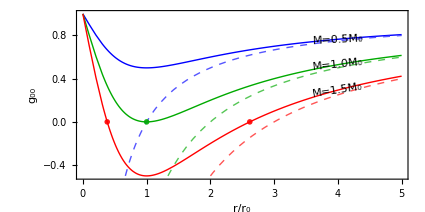

```mathematica
point[color_, xcoord_,ycoord_:0] := Inset[
Graphics@{Opacity[0.9], color, Disk[]},
(* {x,y}, {xOrig,yOrig}, scaling --> see Inset doku *)
{xcoord, ycoord}, {0,0}, 0.07
]
fig = Plot[Evaluate@holoCompareFuncs,
{z,0,5},
PlotRange-> {-0.5,1},
PlotStyle-> holoColors~Join~({Dashed,Lighter@#}&/@holoColors),
FrameLabel->{"r/r_0", "g_00"},
PlotRangePadding-> None,
PlotRangeClipping->False,
Frame-> True,
Epilog-> {
EpiLabels[4, holoGraphs, holoLabels],
(* Roots bestimmt mit First@FindRoot[holoGraphs[#][[3]]&[z],{z,0.5}] *)
(*point[pointColors⟦4⟧, 1],
point[pointColors⟦3⟧,0,1],
point[pointColors⟦2⟧, 2.61803],
point[pointColors⟦1⟧, 0.38196],*)
point[holoColors⟦2⟧, 1],
point[holoColors⟦3⟧, 0.38196],
point[holoColors⟦3⟧, 2.61803]
},
AspectRatio-> 0.5,
ImageSize-> 15cm
]
```

```mathematica
Export["../figures/remnant-plot-holography.pdf", Show@fig]
```

../figures/remnant-plot-holography.pdf

### Alternativplot, der höhere Dimensionen darstellt

Pending Work here

```mathematica
(* Holografie in n dimensionen mit Testmassen und ähnlich C um Subscript[r, 0] gestreckt und so *)
holoN[z_,n_] := z^(2+n)/(z^(2+n) + 1)
holoL[n_] := (1/(1+n))^(1/(2+n))
Mext[n_] = 1/2 ( z^(1+n)/holoN[z,n])/.z-> holoL[n]
g00holoN[z_, M_,n_, func_] := 1 - 2M func[z,n]/z^(1+n)
g00holoN[z, 1,4]

(* Testfunktionen aufbauen *)
maxN = 7;
holoNfuncs =Table[ g00holoN[z*holoL[n],Mext[n],n, holoN], {n,0,maxN}];
STMfuncs = Table[g00holoN[z*holoL[n],Mext[n],n, 1&],{n,0,maxN}];
holoNcompares = Join[STMfuncs,holoNfuncs]

(* Labels *)
maxNlabels = Min[4, maxN];
holoNlabels = Table["n="<>ToString@n, {n,0,maxNlabels-1}]~Join~{"..."}
holoNlabelFuncs[z_] = holoNfuncs⟦1;;maxNlabels+1⟧ /. z-> z;
holoNlabelPos =With[{labelPosFunc = 1-z^2/33+0.1}, (* die kann man auch plotten... *)
RootToSol@FindRoot[labelPosFunc== # ,{z,1}]&/@ holoNlabelFuncs[z]
]
```

1/2 (1/(1+n))^(-1/(2+n)) (1+((1/(1+n))^(1/(2+n)))^(2+n))

g00holoN[z,1,4]

{1-2/z,1-3/z^2,1-4/z^3,1-5/z^4,1-6/z^5,1-7/z^6,1-8/z^7,1-9/z^8,1-(2 z)/(1+z^2),1-(3 z)/(2 (1+z^3/2)),1-(4 z)/(3 (1+z^4/3)),1-(5 z)/(4 (1+z^5/4)),1-(6 z)/(5 (1+z^6/5)),1-(7 z)/(6 (1+z^7/6)),1-(8 z)/(7 (1+z^8/7)),1-(9 z)/(8 (1+z^9/8))}

{n=0,n=1,n=2,n=3,...}

{4.24588,3.39017,2.90755,2.6032,2.39621}

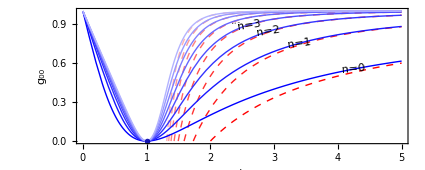

```mathematica
fig=Plot[Evaluate@holoNcompares,
{z,0,5},
PlotRange-> {0,1},
PlotStyle -> Join[
{Dashed,Lighter[Red, 0.7*Rescale[#,{0,maxN}]]}&/@Range[0,maxN],
Lighter[Blue, 0.7*Rescale[#,{0,maxN}]]&/@Range[0,maxN],
{Thick,Darker@Green}
],
(*PlotStyle-> holoColors~Join~({Dashed,Lighter@#}&/@holoColors),*)
FrameLabel->{"r/r_0", "g_00"},
PlotRangePadding-> None,
PlotRangeClipping->False,
Frame-> True,
Epilog-> {
(*MapIndexed[
{Opacity[1-Rescale[First@#2,{0,maxN}]],
#//.(Background->Red)-> (Background->Green)}1&,*)
EpiLabels[holoNlabelPos, holoNlabelFuncs, holoNlabels],
(* Roots bestimmt mit First@FindRoot[holoGraphs[#][[3]]&[z],{z,0.5}] *)
point[Darker@Blue, 1]
},
AspectRatio-> 0.4,
ImageSize-> 15cm
]
```

```mathematica
Export["../figures/remnant-plot-holography-n.pdf", Show@fig]
```

../figures/remnant-plot-holography-n.pdf

## Self-encoding Remnants-Plot

```mathematica
masses = {0.5, 1.0, 1.5};
alphas = {α0(1-1/10), α0, α0(1+1/10)};
ClearAll[halphaGraphs];
halphaGraphs[z_,α_] = Join[g00[z,#,halpha[#,α]&]&/@ masses]; 
halphaCompareFuncs= Flatten[{halphaGraphs[z,α0],SMMGraphs}];
(*halphaCompareFuncs= Flatten[{halphaGraphs[z,#]&/@alphas,SMMGraphs}];*)
```

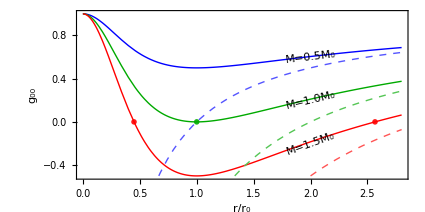

```mathematica
fig = Plot[Evaluate@halphaCompareFuncs,
{z,0,2.8},
PlotRange-> {-0.5,1},
PlotStyle-> holoColors~Join~({Dashed,Lighter@#}&/@holoColors),
FrameLabel->{"r/r_0", "g_00"},
PlotRangePadding-> None,
PlotRangeClipping->False,
Frame-> True,
Epilog-> {
EpiLabels[2, holoGraphs, holoLabels],
(* Roots bestimmt mit FindRoot[halphaGraphs[#,α0][[3]]&[z], {z,2.5}] *)
(*point[pointColors⟦4⟧, 1],
point[pointColors⟦3⟧,0,1],
point[pointColors⟦2⟧, 2.56625],
point[pointColors⟦1⟧, 0.44915],*)
point[holoColors⟦2⟧, 1],
point[holoColors⟦3⟧, 0.44915],
point[holoColors⟦3⟧, 2.56625]
},
AspectRatio-> 0.5,
ImageSize-> 15cm
]
```

```mathematica
Export["../figures/remnant-plot-halpha-alpha0.pdf", Show@fig]
```

../figures/remnant-plot-halpha-alpha0.pdf

### Alternativplot, der den α-Freiheitsgrad darstellt

Zunächst suchen wir Belegungen für α, die bei g00(z=1) eine äquidistante Verteilung der g00-Kurven ermöglichen. Dies geschieht mit einer numerischen Invertierung und anschließender Interpolation zu einer inversen Funktion nach α.

```mathematica
(* g00 mit M=1 und beliebigem α fuer halpha, Abkürzung. *)
g00halpha[z_,α_] = g00[z,1,halpha[#,α]&]
(* g00 an der Stelle z=1 mit M=1 als Funktion von α. *)
funkA[α_] = g00halpha[1,α]
(* Interpolierte inverse Funktion *)
funkAinv = Interpolation@Table[{funkA[a],a},{a,0.001,30, 0.05}]
```

1-(2 (1+1/2 (1/z)^α)^(-3/α))/z

1-2^(1+3/α) 3^(-3/α)

InterpolatingFunction[{{-0.920402,1.}},<>]

```mathematica
numAlphas = 15;
touchedMetricValues = Range[0,1-0.01, 2/numAlphas]
touchedAlphas= Reverse /@ Table[{a,funkAinv[a]},
{a,Join[-Reverse@#, Rest@#]&[touchedMetricValues]} (* baue "symmetrisch" um g00=0 herum. *)
(*{a,-1+0.03, 1-0.01, 2/numAlphas}*)(*<- Alte Wahl, hatte α0 nicht drin. *)
];
colorScale = Lighter[Red, 0.9*Rescale[#,{0,Length@touchedAlphas}]]&/@Reverse@Range@Length@touchedAlphas
```

{0,2/15,4/15,2/5,8/15,2/3,4/5,14/15}

InterpolatingFunction::dmval: Input value {-14/15} lies outside the range of data in the interpolating function. Extrapolation will be used.

{RGBColor[1.,0.9,0.9],RGBColor[1.,0.84,0.84],RGBColor[1.,0.78,0.78],RGBColor[1.,0.72,0.72],RGBColor[1.,0.66,0.66],RGBColor[1.,0.6,0.6],RGBColor[1.,0.54,0.54],RGBColor[1.,0.48,0.48],RGBColor[1.,0.42,0.42],RGBColor[1.,0.36,0.36],RGBColor[1.,0.3,0.3],RGBColor[1.,0.24,0.24],RGBColor[1.,0.18,0.18],RGBColor[1.,0.12,0.12],RGBColor[1.,0.06,0.06]}

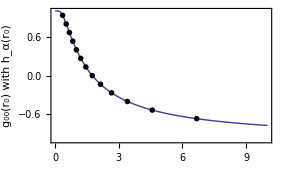

../figures/limit-halpha-plot-alpha-choices.pdf

```mathematica
fig =Show[
Plot[funkA[a],{a,0.01,10}, PlotRange-> {-1,1},
Frame-> True,
ImageSize -> 10cm,
AspectRatio-> 0.6,
PlotRangePadding->None,
FrameLabel-> {"α","g_00(r_0) with h_α(r_0)"}],
(* Selbstgemachten Listplot, inspiriert von h-profiles.nb *)
Graphics@Map[Inset[Graphics@{#⟦1⟧,Disk[], Darker[#⟦1⟧,.5], Circle[]},#⟦2⟧, Center,0.35]&,Transpose@{colorScale,touchedAlphas}]
(* ListPlot[touchedAlphas, PlotMarkers->{Automatic, Medium}] *)
]
Export["../figures/limit-halpha-plot-alpha-choices.pdf",fig]
```

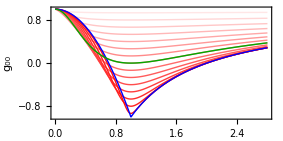

```mathematica
αMax=1000; (* ein "unendlich" grosses letztes α *)
fig=Plot[Evaluate@Join[
Table[g00halpha[z,α] ,{α,Reverse[First /@ touchedAlphas]}],
{g00halpha[z,αMax],g00halpha[z,α0]}
],
{z,0,2.8},
PlotRange-> {-1,1},
FrameLabel->{"r/r_0", "g_00"},
PlotRangePadding-> None,
Frame-> True,
PlotStyle -> Join[colorScale,{{Thick,Blue}, {Thick,Darker@Green}} ],
Epilog-> {
(*EpiLabels[4, holoGraphs, holoLabels],*)
(*point[Darker@Green, 1],*)
},
AspectRatio-> 0.5,
ImageSize-> 10cm
]~Quiet~Power::infy (* komische 1/0-Fehler unterbinden *)
```

```mathematica
Export["../figures/limit-halpha-plot.pdf", Show@fig]
```

../figures/limit-halpha-plot.pdf